# DFT-Tests

Zum numerischen Vergleich/Überprüfung meiner analytisch gewonnenen Fouriertransformationen versuche ich die Diskrete Fourier-Transformation mit analytischen Funktionen zu vergleichen. In diesem Dokument hält dafür die Funktion f(x) statt, die zwar aussieht wie meine Holographie-Profil, aber das ist nur ein konstruiertes Beispiel. Es hat nichts mehr mit meinem Holographie-Zeug zu tun. 
Die hier gemachten 1d-Fouriertrafos ergeben das gleiche Ergebnis wie meine 1d-Python-Scripte.
Offene Fragen sind: Wie kann man (analytisch) Fouriertransform und (numerisch) Fourier im Ergebnis miteinander vergleichen? Wieso landen die Punkte der numerischen Lösung nicht auf der analytischen?

Im Prinzip kann man hier beliebige Funktionen einsetzen, hauptsache halbwegs brauchbare Fouriertrafos (keine MeijerGs und so) kommen da heraus. Bei der Testfunktion, die ich gebastelt habe, ist das schon fast wieder nicht der Fall, da da Diracs und sowas reinkommen.

```mathematica
f[x_] = x^2  / (x^2 + 1)
```

x^2/(1+x^2)

```mathematica
fy[x_] = f[x+5]+f[5-x]-1
ω[p_] = FourierTransform[fy[x],x,p]
```

-1+(5-x)^2/(1+(5-x)^2)+(5+x)^2/(1+(5+x)^2)

√(2 π) DiracDelta[p]-ⅇ^((-1-5 ⅈ) p) (1+ⅇ^(10 ⅈ p)) √(π/2) (ⅇ^(2 p) HeavisideTheta[-p]+HeavisideTheta[p])

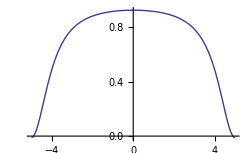
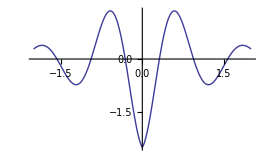
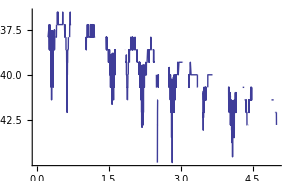

```mathematica
{Plot[fy[x],{x,-5,5}],Plot[ω[p]//Re,{p,-2,2}],Plot[ω[p]//Im // Log, {p,0,5}]}
```

Hervorragendes Zwischenergebnis: Die gerade Funktion erzeugt eine Fouriertrafo mit quasi nur Realteil.

```mathematica
ortsraum = Table[fy[x],{x,-5,5-1}]
```

{-1/101,20/41,51/65,22/25,575/629,12/13,575/629,22/25,51/65,20/41}

```mathematica
(*
ortsraum[[1]] = 0;
ortsraum
Length[ortsraum]
*)
```

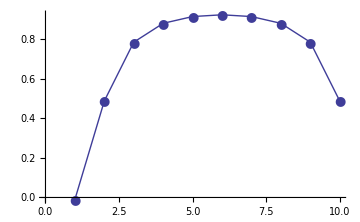

```mathematica
ListLinePlot[ortsraum, PlotMarkers->{Automatic, 13}, ImageSize->Medium]
```

```mathematica
impulsraum = Fourier[ortsraum]
```

{2.22824+0. ⅈ,-0.531822+0. ⅈ,-0.28896+0. ⅈ,-0.162904+0. ⅈ,-0.103231+0. ⅈ,-0.0857161+0. ⅈ,-0.103231+0. ⅈ,-0.162904+0. ⅈ,-0.28896+0. ⅈ,-0.531822+0. ⅈ}

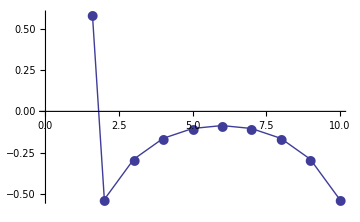
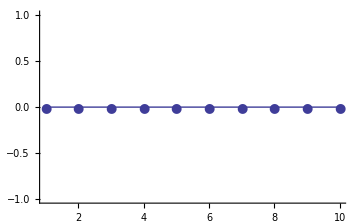

```mathematica
ListLinePlot[impulsraum//#,PlotMarkers-> {Automatic,13},ImageSize-> Medium] &/@{Re,Im}
```

```mathematica
impulsraumEinheiten = Transpose[{
(#&)/@Range[-5,5-1,1],
Re[impulsraum]  }]
```

{{-5,2.22824},{-4,-0.531822},{-3,-0.28896},{-2,-0.162904},{-1,-0.103231},{0,-0.0857161},{1,-0.103231},{2,-0.162904},{3,-0.28896},{4,-0.531822}}

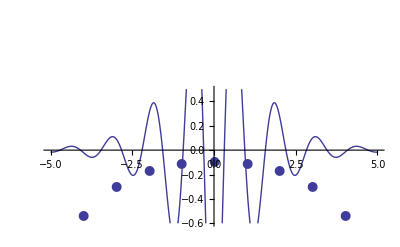

```mathematica
Show[
Plot[Re[ω[ p ]],{p,-5,5}, PlotRange-> {-0.6,0.5} ],
ListPlot[impulsraumEinheiten, PlotMarkers-> {Automatic,13}]
]
```

```mathematica
Manipulate[Show[
Plot[Re[ω[ p ]],{p,-5,5}, PlotRange-> {-0.6,0.5} ],
ListLinePlot[Transpose[{(2 Pi / Length[impulsraum]#&)/@Range[-5,5-1,1], k+Re[impulsraum]  }], PlotMarkers-> {Automatic,13}]
], {k,0,2}]
```